```mathematica
$Path=Prepend[$Path,"E:\\HOME\\anton\\roundabout"];
```

```mathematica
<<"ACPackages`"
<<"ErrorBarPlots`"
```

```mathematica
$WD=SetWorkDir[];
```

```mathematica
$WD=NotebookDirectory[];
```

```mathematica
SetWorkDir["/2006.07.20/Re=10"];
```

```mathematica
(*Table of results: list of {date(year,month,day),mesh(Nx=Nz),Re,r/R,gamma,F(r),Coriolis;shift,mvx,δmvx,mvy,δmvy,mvz,δmvz,Evx,δEvx,Evy,δEvy,Evz,δEvz,mψ,δmψ,comment}*)
indepkol=9;
depkol=15;
```

## Добавление записей

```mathematica
dvx=dvy=dvz=0;
dqvx=dqvy=dqvz=0;
```

```mathematica
{dvx,dvy,dvz,dqvx,dqvy,dqvz}={2 10^-5,1 10^-4,2 10^-5,5 10^-6,2 10^-5,2 10^-6};
```

```mathematica
{dvx,dvy,dvz,dqvx,dqvy,dqvz}={0,6 10^-5,0,0,2 10^-5,0};
```

```mathematica
putlist=Join[{2011,03,02},{128},{Rm=70,kappa=0.975,gamma=10^-4,Fr="dp",Coriolis=0,shift,maxvx,dvx,maxvy,dvy,maxvz,dvz,mqvx,dqvx,mqvy,dqvy,mqvz,dqvz,Max[Abs[ψ]],Max[Abs[ψ2-ψ1]],"ErrScale 1e-4"}]/.b_:>CForm[b]/;NumericQ[b]
```

{2010,12,16,256,115,0.5,0.0001,dp1,0,0.4111946309734112,0.13345372743418532,0.00002,0.5394917991670589,0.0001,0.0939417424156275,0.00002,0.0031174654488904095,5.e-6,0.11665792960566573,0.00002,0.001136343580263234,2.e-6,0.04115338165082248,0.0013980584104512864,ErrScale 1e-4}

```mathematica
putlist>>>($WD<>"\\result.dat")
{Rm,kappa,gamma,Fr,Coriolis,shift,maxvx,dvx,maxvy,dvy,maxvz,dvz,mqvx,dqvx,mqvy,dqvy,mqvz,dqvz,ψ,ψ2,ψ1}=.;
```

## Анализ записей

### Функции

```mathematica
UpdateData:=Block[{},Print[fields=Module[{res,stm},res=ReadList[stm=StringToStream[First[ReadList[$WD<>"\\result.dat"]]],Word,WordSeparators->{" ",",","{","}"}];Close[stm];res]];
all=Select[Rest[ReadList[$WD<>"\\result.dat"]]/.{a_+b_ E->b*10^a}/.{a_+b_ e->b*10^a},StringFreeQ[Last[#],"wrong"]&];
Print["Total:",Length[all]," records"];]
```

```mathematica
MakeRule[el_]:=MapThread[Rule,{fields,el}];
```

```mathematica
ShowDependance[param_,funcs_,conditions_List:{},viv_:True]:=Block[{allbut=GetResults[conditions,viv],dep,deplist,numpar,othern,otherv},If[FreeQ[Drop[fields,{indepkol+1,-2}],param],Print["Wrong parameter"];Return[]];numpar=First[Flatten[Position[fields,param]]];othern=Complement[Join[Range[4,Length[fields]-depkol-1],{Length[fields]}],{numpar}];If[viv,Print["All such parameters=",Union[(#1⟦numpar⟧&)/@allbut]]];dep=First[Rest[Reap[(Sow[#1,NotList@@#1⟦othern⟧]&)/@Sort[allbut,N[#1⟦numpar⟧]<N[#2⟦numpar⟧]&],_,f]]];dep=Select[dep,Length[Last[#1]]>1&];
(*If[viv,Print["dep=",dep]];*)
otherv=Drop[Drop[Drop[fields,{indepkol+1,-2}],{numpar}],3];If[viv,Print[otherv]];nom=0;If[Length[dep]==0,Print["Data was not found"];Return[]];If[viv,Print["Plots can be shown for parameters:"]];(Print["№",++nom,":",MapThread[Rule,{otherv,List@@First[#1]}],", number of points=",Length[Last[#1]]]&)/@dep;If[Length[dep]>1,nom=Input["Введите номер желаемой зависимости"],nom=1];
If[viv,Print["So constant parameters are:\t",Thread[otherv->List@@First[dep⟦nom⟧]]]];deplist=({#1,"δ"<>#1," "<>#1}&)/@Flatten[{funcs}];pts=Join[{param},RotateRight/@deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];pts=Function[l,{({{#1⟦1⟧,#1⟦2⟧},ErrorBar[#1⟦3⟧]}&)/@Flatten/@Transpose[Join[{First/@pts},{l}]],l⟦1,-1⟧}]/@Transpose[deplist/.MakeRule/@Last[dep⟦nom⟧]];
pts=Join[{param},deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];(*If[param≠Last[fields],(ListPlot[{First[#1]},AxesLabel->{param,Last[#1]},Axes->True,Frame->False,PlotLabel->Last[#1],PlotMarkers->{■}]&)/@pts];*)
If[param≠Last[fields],ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All]&/@Transpose[pts[[All,2;;-2]]]
]
];
```

```mathematica
ShowDependanceMod[param_,funcs_,conditions_List:{}]:=Block[{allbut=GetResults[conditions],(*dep,deppfin,*)deplist,numpar,othern,otherv},
numpar=First[Flatten[Position[fields,param]]];othern=Complement[Join[Range[4,Length[fields]-depkol-1],{Length[fields]}],{numpar}];dep=First[Rest[Reap[(Sow[#1,NotList@@#1⟦othern⟧]&)/@Sort[allbut,N[#1⟦numpar⟧]<N[#2⟦numpar⟧]&],_,f]]];dep=Select[dep,Length[Last[#1]]>1&];
otherv=Drop[Drop[Drop[fields,{indepkol+1,-2}],{numpar}],3];nom=0;If[Length[dep]==0,Print["Data was not found"];Return[]];(Print["№",++nom,":",MapThread[Rule,{otherv,List@@First[#1]}],", number of points=",Length[Last[#1]]]&)/@dep;
(*depfin=dep[[1]]; Тупой выбор первого набора. Надо бы научиться выбирать с наилучшей точностью*)
depfin=Prepend[f[Join@@(First/@Rest/@dep)],dep[[1,1]]];(*Объединение всех данных*)
deplist=({#1,"δ"<>#1," "<>#1}&)/@Flatten[{funcs}];pts=Join[{param},RotateRight/@deplist,{"comment"}]/.MakeRule/@Last[depfin];pts=Function[l,{({{#1⟦1⟧,#1⟦2⟧},ErrorBar[#1⟦3⟧]}&)/@Flatten/@Transpose[Join[{First/@pts},{l}]],l⟦1,-1⟧}]/@Transpose[deplist/.MakeRule/@Last[depfin]];
pts=Join[{param},deplist,{"comment"}]/.MakeRule/@Last[depfin];(*If[param≠Last[fields],(ListPlot[{First[#1]},AxesLabel->{param,Last[#1]},Axes->True,Frame->False,PlotLabel->Last[#1],PlotMarkers->{■}]&)/@pts];*)
If[param≠Last[fields],Sow[ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All],StringDrop[#⟦-1,-1⟧,1]]&/@Transpose[pts[[All,2;;-2]]]
]
];
```

```mathematica
GetResults[conditions_List:{},viv_:False]:=Block[{pattern,rules=Union[Select[conditions,Head[#]==Rule&]],
(*Unequal doesn't work always*)
ineqs=And@@Flatten[Select[conditions,MemberQ[{Less,LessEqual,Greater,GreaterEqual,Unequal},Head[#]]∨#==False&]]},
MatchesQ[el_]:=Module[{mr=MakeRule[el]},Simplify[ineqs/.mr]∧Complement[rules,mr]=={}];
If[viv,Print["All data matches (",Simplify[ineqs],")",Sequence@@("&&("<>First[#]<>"="<>ToString[InputForm[Last[#]]]<>")"&/@rules),":"]];
Return[Select[all,MatchesQ]];
];
```

```mathematica
(*Этой версией пользоваться только для списка,задающего однозначную зависимость!*)
FilterWrong[list_List,x_String,y_String]:=Block[{cands,posx=Position[fields,x],posy=Position[fields,y],badpars,bad,good},
If[Length[posx]<1,Print["Didn't find parameter ",x];Return[$Failed],posx=posx[[1,1]]];
If[Length[posy]<1,Print["Didn't find parameter ",y];Return[$Failed],posy=posy[[1,1]]];
cands=Select[list,StringFreeQ[GetField[#,"comment"],"wrong"]&];
cands=GetFields[#,{x,y,"δ"<>y}]&/@cands;
good=First/@Select[Tally[cands,First[#1]==First[#2]&],Last[#]==1&];
Print[ "Параметры в единственном варианте: ",good];
bad=Select[Tally[cands,First[#1]==First[#2]&],Last[#]>1&];
badpars=First/@First/@bad;
Print["Параметры нуждаются в выборе: ",badpars];
Print["Отфильтровано ",Total[Last/@bad]-Length[bad]," записей с большей погрешностью"];
SortBy[Join[Function[par,First@Select[list,#[[posx]]==par[[1]]&]]/@good,Function[par,First@SortBy[Select[list,#[[posx]]==par&],#[[posy+1]]&]]/@badpars],#[[posx]]&]
]
(*Это универсальная чистка*)
FilterWrong[list_List,y_String]:=Block[{cands,posy=Position[fields,y],badpars,bad,good},
If[Length[posy]<1,Print["Didn't find parameter ",y];Return[$Failed],posy=posy[[1,1]]];
cands=Select[list,StringFreeQ[GetField[#,"comment"],"wrong"]&];
cands=Join[Take[#,{1,indepkol}],GetFields[#,{y,"δ"<>y}]]&/@cands;
good=Take[#[[1]],{5,indepkol}]&/@Select[Tally[cands,Take[#1,{5,indepkol}]==Take[#2,{5,indepkol}]&],Last[#]==1&];
Print[ "Параметры в единственном варианте: ",good];
bad=Select[Tally[cands,Take[#1,{5,indepkol}]==Take[#2,{5,indepkol}]&],Last[#]>1&];
badpars=Take[#[[1]],{5,indepkol}]&/@bad;
Print["Параметры нуждаются в выборе: ",badpars];
Print["Отфильтровано ",Total[Last/@bad]-Length[bad]," записей с большей погрешностью"];
(*Сначала по размеру сетки, потом по погрешности, потом по дате*)
SortBy[Join[Function[par,First@Select[list,Take[#,{5,indepkol}]==par&]]/@good,Function[par,First@SortBy[Select[list,Take[#1,{5,indepkol}]==par&],#[[posy+1]]&]]/@badpars],Take[#1,indepkol]&]
]
```

### Действия

```mathematica
UpdateData
```

{year,month,day,Nxz,Re,r/R,gamma,F(r),Coriolis,shift,mvx,δmvx,mvy,δmvy,mvz,δmvz,Evx,δEvx,Evy,δEvy,Evz,δEvz,mψ,δmψ,comment}

Total:686 records

```mathematica
$res=GetResults[{"Nxz"->256,"r/R"->0.3,"F(r)"->"1"}];Length[$res]
First[$res]
```

24

{2014,1,11,256,5,0.3,0.0001,1,0,-0.029428,0.0202976,2.41×10^-9,0.984368,7.94×10^-13,0.0111033,3.13×10^-9,0.0000566398,9.58×10^-13,0.254156,1.7×10^-14,0.0000191782,1.71×10^-12,0.00549931,0.000133805,ErrScale 1e-4}

```mathematica
$res=GetResults[{}];Length[$res]
```

686

```mathematica
$res=GetResults[{"F(r)"->"dp","r/R"->0.9}];Length[$res]
```

28

```mathematica
$res=GetResults[{"F(r)"->"r"}];Length[$res]
```

182

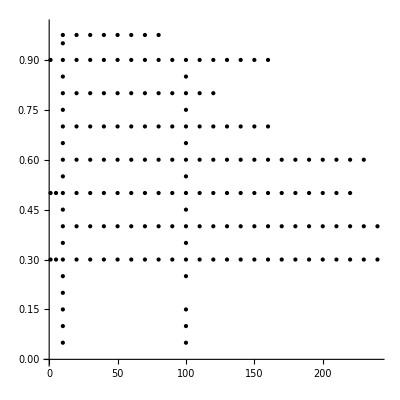

```mathematica
Graphics[Point/@Union[GetFields[#,{"Re","r/R"}]&/@$res],AspectRatio->1,Axes->True,AxesOrigin->{0,0},PlotRange->{0,1}]
```

```mathematica
(*const*)
plus=Graphics[Join[Point/@{{100,0.65},{200,0.9},{200,0.95}},{Line[{{210,0.9},{300,0.9}}],Line[{{250,0.05},{300,0.05}}],Line[{{90,0.975},{300,0.975}}],Line[{{300,0.05},{300,0.975}}]}]]
```

```mathematica
(*gradient*)
plus=Graphics[Join[Point/@{{150,0.05},{160,0.05},{170,0.05},{180,0.05},{190,0.05},{200,0.05},{200,0.3}},{Line[{{240,0.05},{300,0.05}}],Line[{{230,0.5},{300,0.5}}],Line[{{1,0.975},{300,0.975}}],Line[{{300,0.05},{300,0.975}}],Line[{{220,0.9},{300,0.9}}],Line[{{240,0.3},{300,0.3}}]}]];
```

```mathematica
(*eps*)
plus=Graphics[Join[Point/@{{200,0.35},{200,0.45},{200,0.55}},{Line[{{170,0.9},{300,0.9}}],Line[{{200,0.05},{200,0.25}}],Line[{{1,0.05},{300,0.05}}],Line[{{90,0.975},{300,0.975}}],Line[{{200,0.65},{200,0.975}}],Line[{{250,0.3},{300,0.3}}],Line[{{230,0.5},{300,0.5}}],Line[{{300,0.05},{300,0.975}}]}]];
```

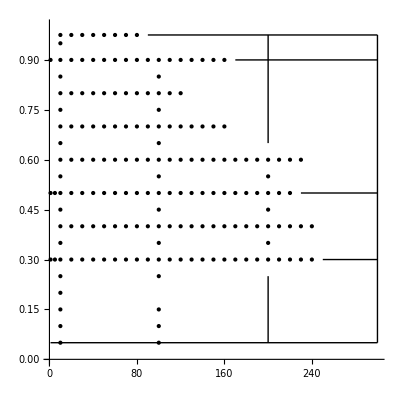

```mathematica
Show[%,plus]
```

```mathematica
Eustice1910=Line[{#/2,√(0.0735/π)/2.59}&/@{20,5000}];
Grindley1908=Line[{#/2,0.317/36.6}&/@{25,1400}];
WhiteII=Line[{#/2,0.630/31.7}&/@{16,13000}];
WhiteI=Line[{#/2,1.032/15.62}&/@{0.058,41000}];
WhiteIII=Line[{#/2,0.2908/610.5}&/@{220,4000}];
```

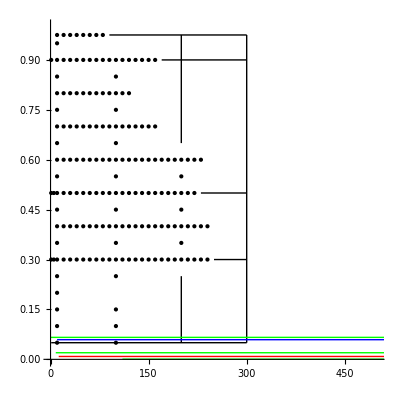

```mathematica
Show[%25,Graphics[{Blue,Eustice1910,Red,Grindley1908,Green,WhiteI,WhiteII,WhiteIII}],PlotRange->{{0,500},{0,1}}]
```

```mathematica
all
```

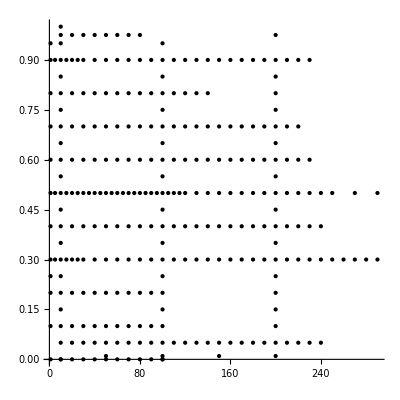

```mathematica
F=1
```

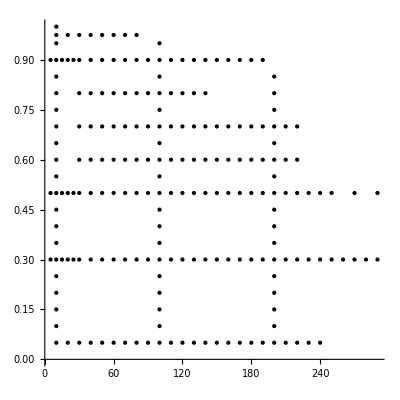

```mathematica
F=dp
```

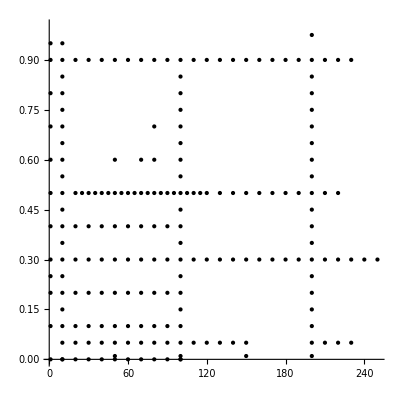

```mathematica
F = r
```

```mathematica
Union[First[#]&/@Union[GetFields[#,{"Re","r/R"}]&/@GetResults[{}]]]
```

{1,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,130,140,150,160,170,180,190,200,210,220,230,240}

```mathematica
Union[4First[#] √(2Last[#])&/@Union[GetFields[#,{"Re","r/R"}]&/@$res]]
```

{15.4919,20.,26.8328,30.9839,40.,46.4758,53.6656,55.857,60.,61.9677,77.4597,80.,80.4984,92.9516,100.,107.331,111.714,120.,123.935,131.453,134.164,141.986,151.789,154.919,160.,160.997,167.571,175.271,185.903,189.315,200.,202.386,214.663,216.887,219.089,223.428,236.643,240.,247.871,252.982,262.907,268.328,278.855,279.285,280.,283.972,303.579,306.725,309.839,320.,321.994,331.3,335.142,340.823,350.542,354.175,360.,371.806,375.659,378.629,390.999,394.36,400.,402.79,404.772,425.958,429.325,433.774,438.178,440.,446.856,455.368,464.758,473.286,480.,481.996,482.991,495.742,505.964,520.,520.615,525.814,526.726,536.656,556.561,557.71,560.,567.944,569.631,588.693,590.322,600.,607.157,613.449,615.272,619.677,640.,643.988,650.661,657.267,657.754,662.601,680.,681.645,697.653,701.085,708.35,709.93,712.629,720.,743.613,744.903,751.319,757.258,760.,774.597,788.72,800.,804.587,804.984,805.581,832.538,836.564,840.,851.915,858.65,867.548,876.356,880.,898.532,899.244,912.316,920.,920.174,946.573,960.,963.992,965.981,993.901,1000.,1019.65,1041.23,1080.,1160.}

```mathematica
$res=GetResults[{"r/R">0.1,"Re"->1,"F(r)"->"dp"}]
```

```mathematica
ShowTable[GetResults[{"Re"->100,"F(r)"->"dp","r/R"->0.5}],{"year","month","day","Nxz","Re","r/R","F(r)","shift","mvx","mvy","mvz","Evx","Evy","Evz","mψ","δmψ"}]
```

#### Зависимость от Дина и не только

```mathematica
ParametricPlot3D
```

```mathematica
resBounds=Join[Table[{1,k},{k,0,1,0.1}],Table[{100,k},{k,0,1,0.1}],Table[{200,k},{k,0,1,0.1}],Table[{R,0},{R,1,250,50}],Table[{R,0.99},{R,1,250,5}],Table[{R,0.5},{R,1,250,50}]];
```

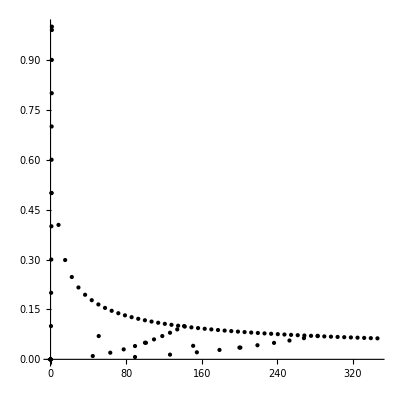

```mathematica
Graphics[Point[{First[#] √(2Last[#]),Last[#]/√First[#]}]&/@resBounds,AspectRatio->1,Axes->True,AxesOrigin->{0,0},PlotRange->{0,1}]
```

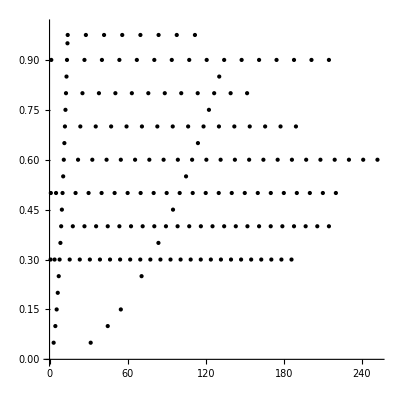

```mathematica
Graphics[Point[{First[#] √(2Last[#]),Last[#]}]&/@Union[GetFields[#,{"Re","r/R"}]&/@$res],AspectRatio->1,Axes->True,AxesOrigin->{0,0},PlotRange->{0,1}]
```

```mathematica
Select[{First[#] √(2Last[#]),Last[#]}&/@Union[GetFields[#,{"Re","r/R"}]&/@$res],Abs[First[#]-70]<5&]
```

{{67.082,0.9},{70.,0.5},{71.5542,0.4},{69.7137,0.3},{70.7107,0.25},{66.4078,0.05},{69.5701,0.05},{72.7324,0.05}}

```mathematica
SortBy[{First[#]/(√(2Last[#])),Last[#]}&/@%,Last]
```

{{210.,0.05},{220.,0.05},{230.,0.05},{100.,0.25},{90.,0.3},{80.,0.4},{70.,0.5},{50.,0.9}}

```mathematica
Select[$res,GetFields[#,{"Re","r/R"}]=={210.,0.05}&]
```

{{2009,5,4,128,210,0.05,0.0001,dp,0,0.466257,0.0539125,8.×10^-7,0.77656,9.×10^-6,0.0351248,2.×10^-6,0.000551769,2.×10^-8,0.177361,5.×10^-6,0.000192523,1.×10^-8,0.0175044,0.00175037,ErrScale 1e-4}}

```mathematica
FrameLabel->{"Dean","Re/(√κ)"}
```

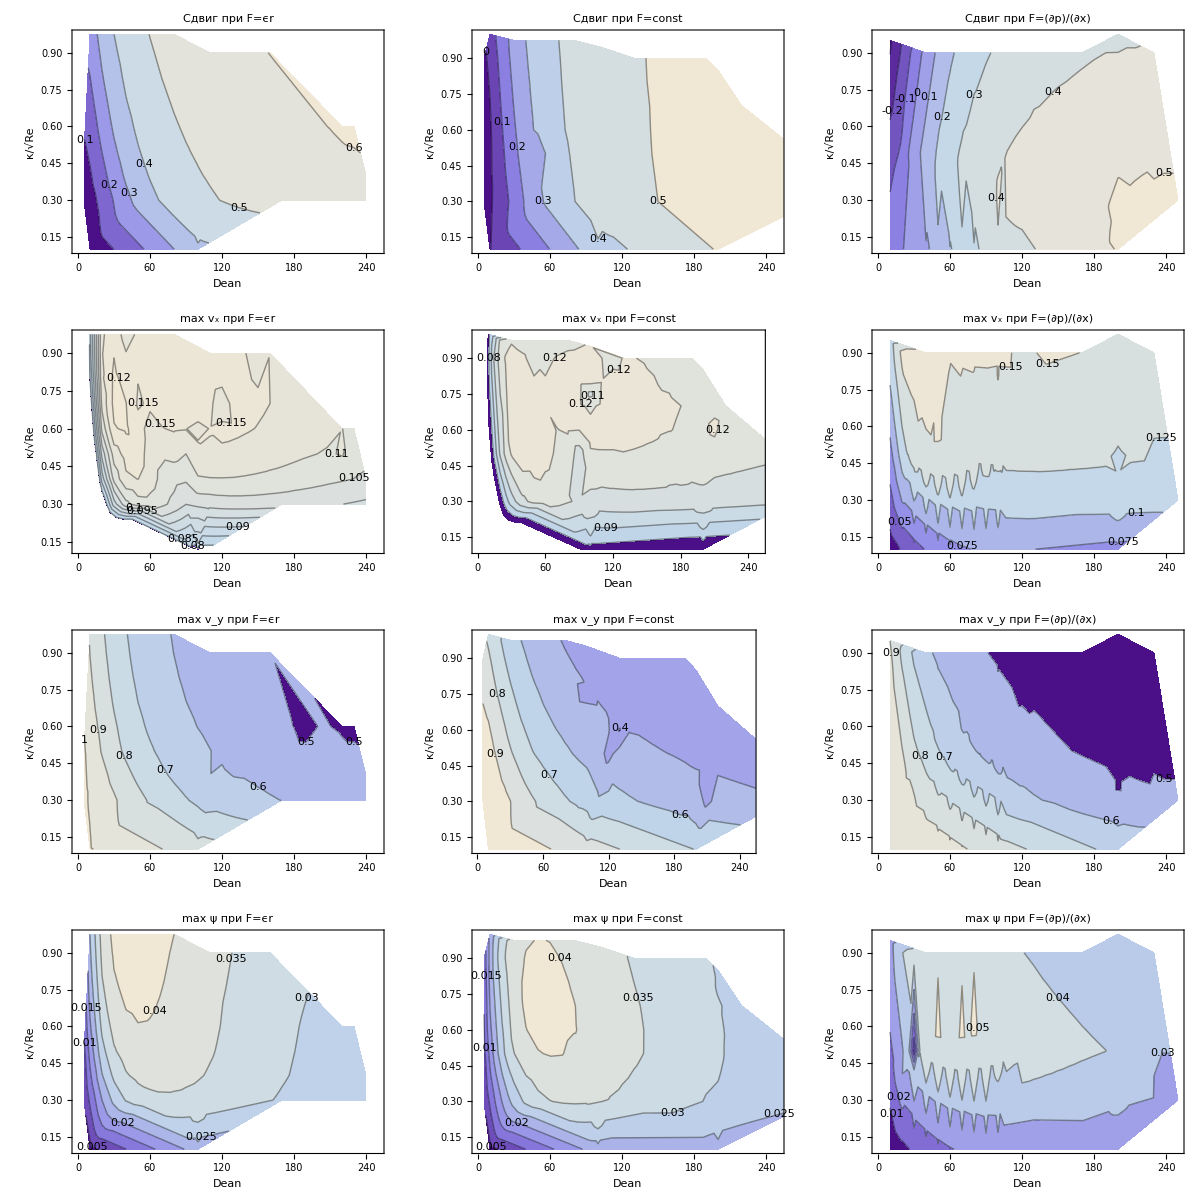

```mathematica
maps=Grid@Table[ListContourPlot[Function[elem,{re,shift,kappa}=elem;{re(√(2kappa))^0
,kappa/(√re)^0,shift}]/@Union[GetFields[#,{"Re",{"shift","mvx","mvy","mψ"}⟦i⟧,"r/R"}]&/@GetResults[{"F(r)"->{"r","1","dp"}⟦k⟧,"r/R">0.05,"Re">1}]],PlotLabel->{"Сдвиг","max v_x","max v_y","max ψ"}⟦i⟧<>" при F="<>{"ϵr","const","(∂p)/(∂x)"}⟦k⟧,PlotRange->{{0,250},All},FrameLabel->{"Dean","κ/√Re"},ContourLabels->All],{i,1,4},{k,1,3}]
```

```mathematica
SetDirectory["d:\\Работа\\бюрократия\\конференции\\Гидродинамические чтения-2018\\report\\pics\\3\\"]
```

d:\Работа\бюрократия\конференции\Гидродинамические чтения-2018\report\pics\3

```mathematica
Monitor[
Do[Export["MapRek"<>{"shift","maxvx","maxv","psi"}[[i]]<>{"eps","const","grad"}[[k]]<>".eps",maps[[1,i,k]],ImageSize->200,ImageResolution->150],{i,1,4},{k,1,3}],{i,k}]
```

```mathematica
Map[ListContourPlot[Function[elem,{re,shift,kappa}=elem;{re √(2kappa),kappa/(√re),shift}]/@Union[Function[res,GetFields[res,{"Re","shift","r/R"}]]/@GetResults[{"F(r)"->#2}]],PlotLabel->Switch[#1,"shift","Сдвиг","mvx","max v_x","mvy","max v_y","mψ","max ψ",_,#1]<>" при F="<>Switch[#2,"r","ϵr","1","const","dp","(∂p)/(∂x)",_,#2],PlotRange->{{0,250},All},FrameLabel->{"Dean","Re/(√κ)"},ContourLabels->All]&@@#&,Outer[List,{"shift","mvx","mvy","mψ"},{"r","1","dp"}],{2}]
```

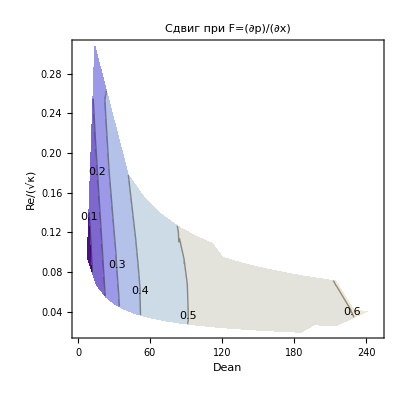

```mathematica
ListContourPlot[{First[#] √(2Last[#]),Last[#]/(√First[#]),#[[2]]}&/@Union[GetFields[#,{"Re","shift","r/R"}]&/@GetResults[{"F(r)"->"r"}]],PlotLabel->"Сдвиг при F=(∂p)/(∂x)",PlotRange->{{0,250},All},FrameLabel->{"Dean","Re/(√κ)"},ContourLabels->All]
```

```mathematica
Show[%36,PlotRange->{{0,250},{0,1}}]
```

```mathematica
GraphicsGrid[{{%49,%50,%51},{%57,%58,%59},{%53,%54,%55}}]
```

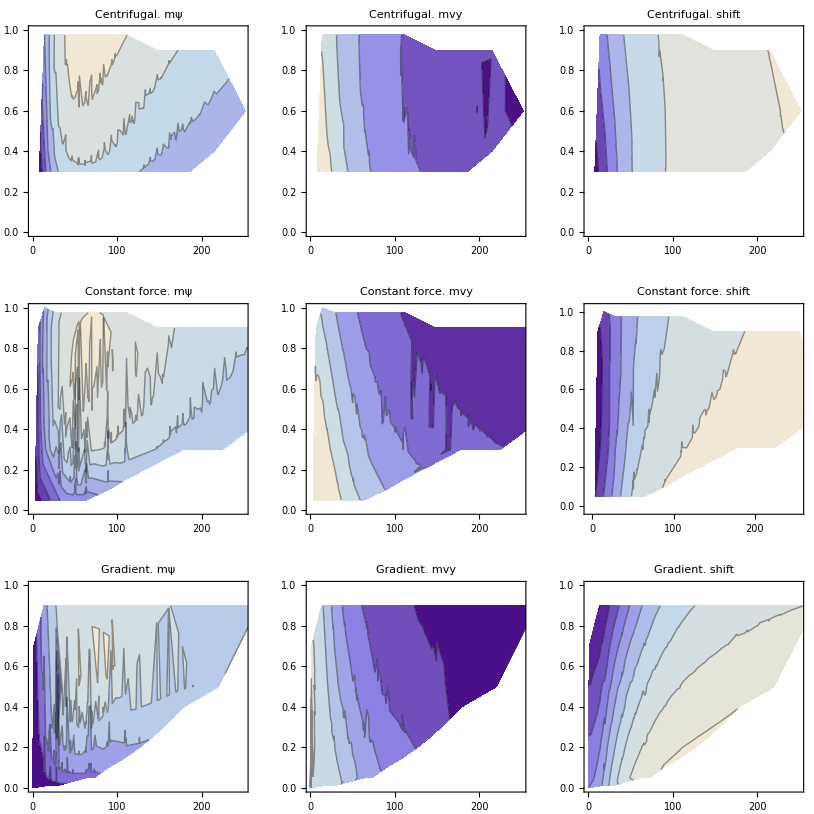

```mathematica
Max@Flatten[Union[GetFields[#,{"shift"}]&/@$res]]
```

0.576232

#### Все поля определённого типа

```mathematica
GetField[res_,field_String]:=Block[{num=Position[fields,field]},
If[Length[num]<1,Print["Field \""<>field<>"\" not found"];Return[$Failed]];
Extract[res,First[num]]
]
GetFields[res_,fs_List]:=GetField[res,#]&/@fs
ShowTable[fromres_,fs_List]:=Prepend[GetFields[#,fs]&/@fromres,fs]//TableForm
```

```mathematica
GetField[Union/@Transpose[$res],"F(r)"]
```

{1,dp,dp1,epsr}

```mathematica
MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res]}]//TableForm
```

```mathematica
Select[MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res]}],Length[#]>3&]//TableForm
```

### Фильтрация

```mathematica
Length[FilterWrong[all,"mvy"]]
```

Параметры нуждаются в выборе: {{1,0,0.0001,dp,0},{1,0.1,0.0001,dp,0},{1,0.2,0.0001,dp,0},{1,0.3,0.0001,dp,0},{1,0.4,0.0001,dp,0},{1,0.5,0.0001,dp,0},{10,0,0.0001,dp,0},{10,0.1,0.0001,dp,0},{10,0.2,0.0001,dp,0},{10,0.3,0.0001,dp,0},{10,0.4,0.0001,dp,0},{10,0.5,0.0001,dp,0},{30,0.5,0.0001,dp,0},{40,0.1,0.0001,dp,0},{40,0.2,0.0001,dp,0},{40,0.5,0.0001,dp,0},{20,0.5,0.0001,dp,0},{70,0,0.0001,dp,0},{70,0.1,0.0001,dp,0},{1,0.25,0.0001,dp,0},{50,0.5,0.0001,dp,0},{60,0.5,0.0001,dp,0},{70,0.5,0.0001,dp,0},{80,0.5,0.0001,dp,0},{90,0.5,0.0001,dp,0},{10,0.05,0.0001,dp,0},{100,0,0.0001,dp,0},{100,0.1,0.0001,dp,0},{100,0.2,0.0001,dp,0},{100,0.3,0.0001,dp,0},{100,0.4,0.0001,dp,0},{100,0.5,0.0001,dp,0},{100,0.05,0.0001,dp,0},{110,0.5,0.0001,dp,0},{200,0.05,0.0001,dp,0},{200,0.5,0.0001,dp,0},{10,0.6,0.0001,dp,0},{10,0.5,0.0001,r,0},{20,0.5,0.0001,r,0},{30,0.5,0.0001,r,0},{40,0.5,0.0001,r,0},{50,0.5,0.0001,r,0},{50,0.5,0.0001,1,0},{30,0.5,0.0001,1,0},{80,0.5,0.0001,1,0},{90,0.5,0.0001,1,0},{100,0.5,0.0001,1,0},{110,0.5,0.0001,1,0},{120,0.5,0.0001,1,0},{100,0.6,0.0001,1,0},{200,0.6,0.0001,1,0},{100,0.7,0.0001,1,0},{160,0.7,0.0001,1,0},{220,0.7,0.0001,1,0},{30,0.9,0.0001,1,0},{50,0.9,0.0001,1,0},{120,0.9,0.0001,1,0},{10,0.9,0.0001,r,0},{10,0.8,0.0001,r,0},{10,0.7,0.0001,r,0},{100,0.6,0.0001,r,0},{80,0.5,0.0001,r,0},{10,0.9,0.0001,dp,0},{100,0.9,0.0001,dp,0},{120,0.9,0.0001,dp,0},{200,0.9,0.0001,dp,0},{10,0.3,0.0001,1,0},{100,0.3,0.0001,1,0},{210,0.3,0.0001,1,0},{250,0.5,0.0001,1,0},{100,0.05,0.0001,1,0},{100,0.4,0.0001,1,0},{200,0.05,0.0001,1,0},{10,0.05,0.0001,1,0},{10,0.4,0.0001,1,0},{100,0.2,0.0001,1,0},{100,0.75,0.0001,1,0},{200,0.85,0.0001,1,0},{70,0.05,0.0001,1,0},{80,0.05,0.0001,1,0},{140,0.05,0.0001,1,0}}

Отфильтровано 108 записей с большей погрешностью

578

```mathematica
FilterWrong[Select[all,Take[#,{5,indepkol}]=={140,0.05,0.0001,"1",0}&],"shift"]
```

Field "δshift" not found

Field "δshift" not found

Параметры в единственном варианте: {}

Параметры нуждаются в выборе: {{140,0.05,0.0001,1,0}}

Отфильтровано 1 записей с большей погрешностью

{{2014,12,3,256,140,0.05,0.0001,1,0,0.497064,0.0501642,0.0000999,0.738309,0.000393,0.0341207,0.0000672,0.000495366,1.92×10^-6,0.160241,0.000162,0.000176094,6.83×10^-7,0.016756,0.000488968,ErrScale 1e-4}}

```mathematica
$badpars=Take[First[#],{5,indepkol}]&/@Select[Tally[all,Take[#1,{5,indepkol}]==Take[#2,{5,indepkol}]&],Last[#]>1&]
```

{{1,0,0.0001,dp,0},{1,0.1,0.0001,dp,0},{1,0.2,0.0001,dp,0},{1,0.3,0.0001,dp,0},{1,0.4,0.0001,dp,0},{1,0.5,0.0001,dp,0},{10,0,0.0001,dp,0},{10,0.1,0.0001,dp,0},{10,0.2,0.0001,dp,0},{10,0.3,0.0001,dp,0},{10,0.4,0.0001,dp,0},{10,0.5,0.0001,dp,0},{30,0.5,0.0001,dp,0},{40,0.1,0.0001,dp,0},{40,0.2,0.0001,dp,0},{40,0.5,0.0001,dp,0},{20,0.5,0.0001,dp,0},{70,0,0.0001,dp,0},{70,0.1,0.0001,dp,0},{1,0.25,0.0001,dp,0},{50,0.5,0.0001,dp,0},{60,0.5,0.0001,dp,0},{70,0.5,0.0001,dp,0},{80,0.5,0.0001,dp,0},{90,0.5,0.0001,dp,0},{10,0.05,0.0001,dp,0},{100,0,0.0001,dp,0},{100,0.1,0.0001,dp,0},{100,0.2,0.0001,dp,0},{100,0.3,0.0001,dp,0},{100,0.4,0.0001,dp,0},{100,0.5,0.0001,dp,0},{100,0.05,0.0001,dp,0},{110,0.5,0.0001,dp,0},{200,0.05,0.0001,dp,0},{200,0.5,0.0001,dp,0},{10,0.6,0.0001,dp,0},{10,0.5,0.0001,r,0},{20,0.5,0.0001,r,0},{30,0.5,0.0001,r,0},{40,0.5,0.0001,r,0},{50,0.5,0.0001,r,0},{50,0.5,0.0001,1,0},{30,0.5,0.0001,1,0},{80,0.5,0.0001,1,0},{90,0.5,0.0001,1,0},{100,0.5,0.0001,1,0},{110,0.5,0.0001,1,0},{120,0.5,0.0001,1,0},{100,0.6,0.0001,1,0},{200,0.6,0.0001,1,0},{100,0.7,0.0001,1,0},{160,0.7,0.0001,1,0},{220,0.7,0.0001,1,0},{30,0.9,0.0001,1,0},{50,0.9,0.0001,1,0},{120,0.9,0.0001,1,0},{10,0.9,0.0001,r,0},{10,0.8,0.0001,r,0},{10,0.7,0.0001,r,0},{100,0.6,0.0001,r,0},{80,0.5,0.0001,r,0},{10,0.9,0.0001,dp,0},{100,0.9,0.0001,dp,0},{120,0.9,0.0001,dp,0},{200,0.9,0.0001,dp,0},{10,0.3,0.0001,1,0},{100,0.3,0.0001,1,0},{210,0.3,0.0001,1,0},{250,0.5,0.0001,1,0},{100,0.05,0.0001,1,0},{100,0.4,0.0001,1,0},{200,0.05,0.0001,1,0},{10,0.05,0.0001,1,0},{10,0.4,0.0001,1,0},{100,0.2,0.0001,1,0},{100,0.75,0.0001,1,0},{200,0.85,0.0001,1,0},{70,0.05,0.0001,1,0},{80,0.05,0.0001,1,0},{140,0.05,0.0001,1,0}}

```mathematica
Manipulate[ShowTable[Select[GetResults[{"F(r)"->"dp"}],Take[#,{5,indepkol}]==$badpars[[i]]&],{"year","month","day","Nxz","Re","r/R","F(r)","shift","mvx","mvy","δmvy","mvz","Evx","Evy","δEvy","Evz","mψ","δmψ"}],{i,1,Length[$badpars],1}]
```

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{F(r)→dp},{5,indepkol}].

Part::partd: Part specification $badpars⟦5⟧ is longer than depth of object.

### Зависимости

```mathematica
allfuncs=Select[Take[fields,{indepkol+1,-2}],Length[StringPosition[#,"δ"]]==0&]
```

{shift,mvx,mvy,mvz,Evx,Evy,Evz,mψ}

```mathematica
ShowDependance["Re",allfuncs,{"F(r)"->"dp","r/R"->0.9}]
```

All data matches (True)&&(F(r)="dp")&&(r/R=0.9):

All such parameters={1,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230}

{Nxz,r/R,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→256,r/R→0.9,gamma→0.0001,F(r)→dp,Coriolis→0,comment→ErrScale 1e-4}, number of points=24

№2:{Nxz→512,r/R→0.9,gamma→0.0001,F(r)→dp,Coriolis→0,comment→ErrScale 1e-4}, number of points=4

So constant parameters are:	{Nxz→512,r/R→0.9,gamma→0.0001,F(r)→dp,Coriolis→0,comment→ErrScale 1e-4}

```mathematica
MapThread[Show[#1,#2]&,{%,%%}]
```

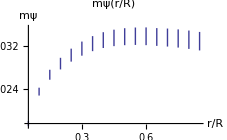
```mathematica
Show[-Graphics-,PlotRange->Automatic,AxesOrigin->{0,0}]
```

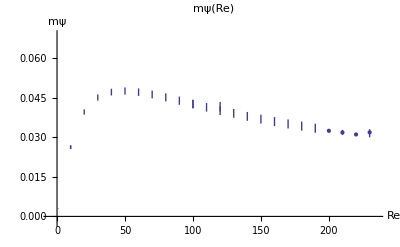
```mathematica
Export["d:\\psiRe9.eps",-Graphics-]
```

d:\psiRe9.eps

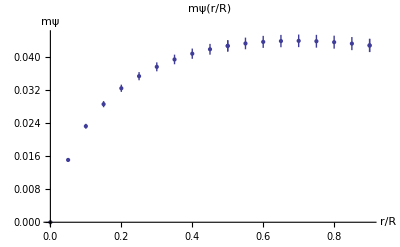
```mathematica
Export["d:\\psik100.eps",-Graphics-]
```

d:\psik100.eps

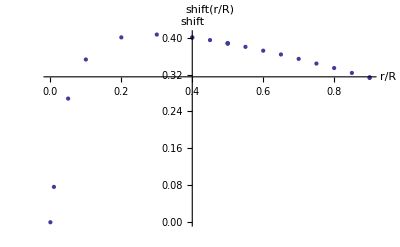
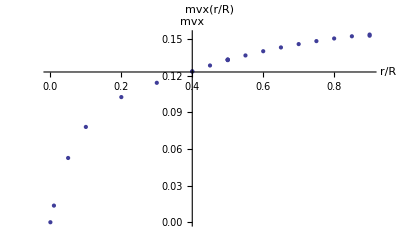
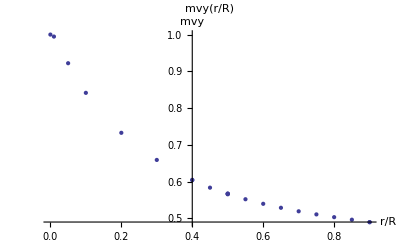
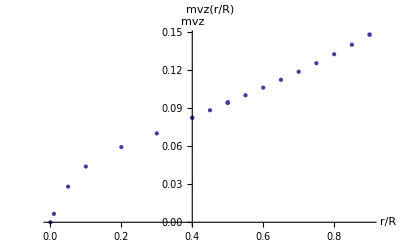
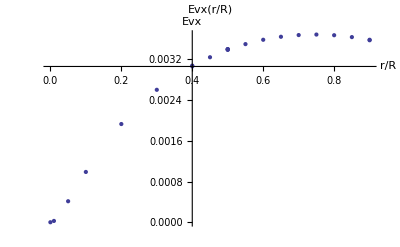
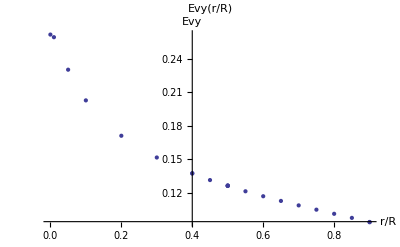
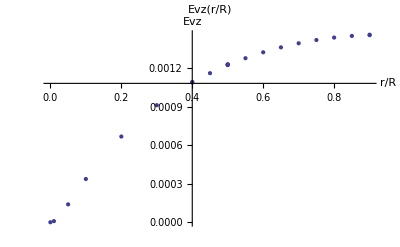
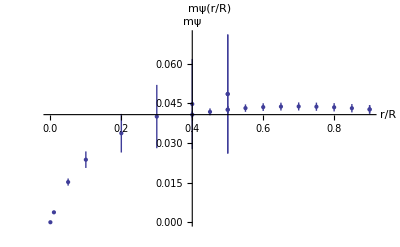

```mathematica
"Re=100;F=dp"
```

All data matches (True)&&(F(r)="dp")&&(Re=200):

All such parameters={0.01,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.975}

{Nxz,Re,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→128,Re→200,gamma→0.0001,F(r)→dp,Coriolis→0,comment→ErrScale 1e-4}, number of points=3

№2:{Nxz→256,Re→200,gamma→0.0001,F(r)→dp,Coriolis→0,comment→ErrScale 1e-4}, number of points=18

№3:{Nxz→512,Re→200,gamma→0.0001,F(r)→dp,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

So constant parameters are:	{Nxz→256,Re→200,gamma→0.0001,F(r)→dp,Coriolis→0,comment→ErrScale 1e-4}

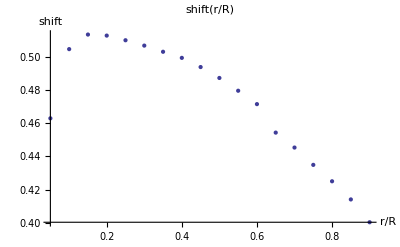
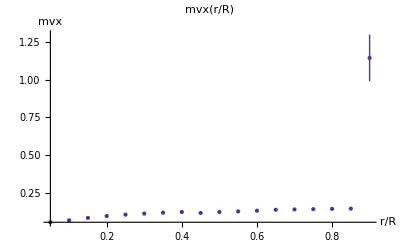
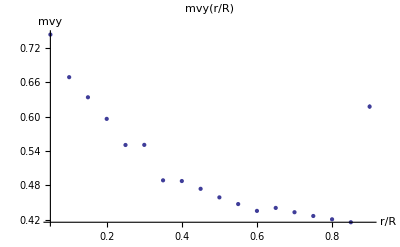
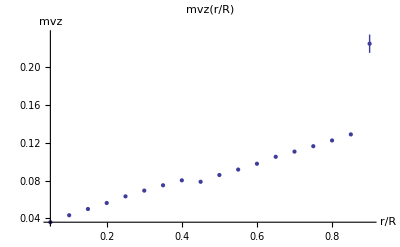
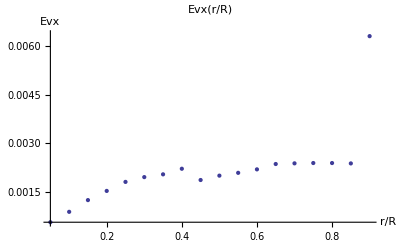
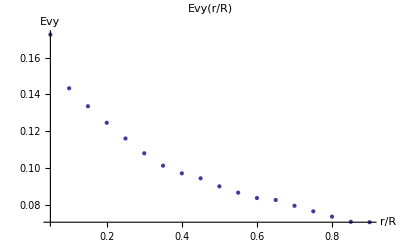
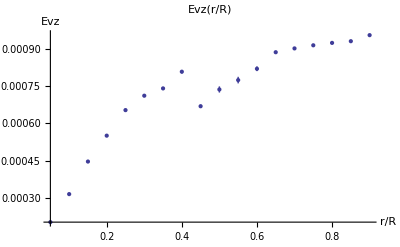
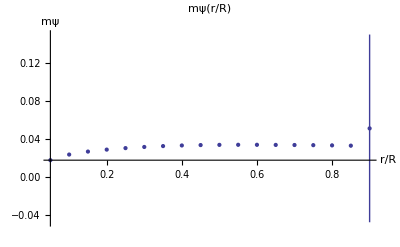

```mathematica
ShowDependance["r/R",allfuncs,{"F(r)"->"dp","Re"->200}]
```

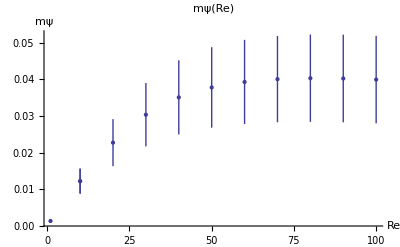
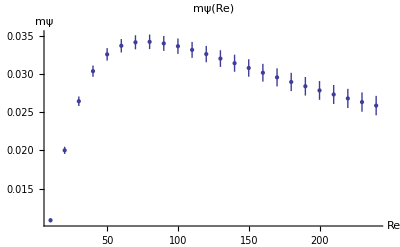
```mathematica
Show[-Graphics-,-Graphics-]
```

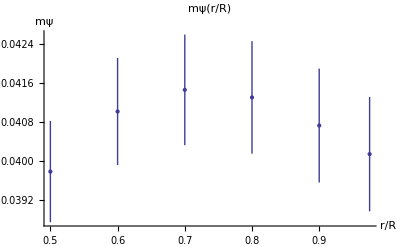
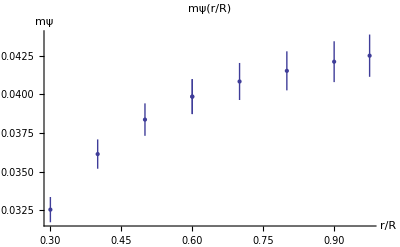
```mathematica
Show[-Graphics-,-Graphics-]
```

#### Результаты

"F(r)=1; Re=50"

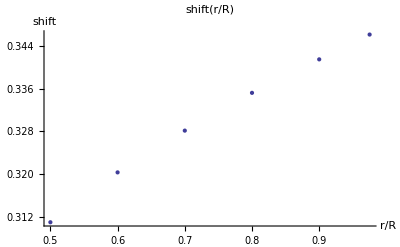
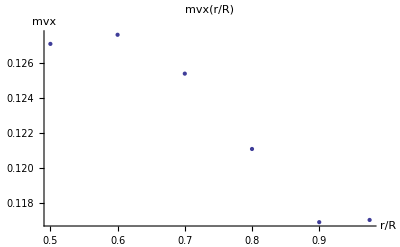
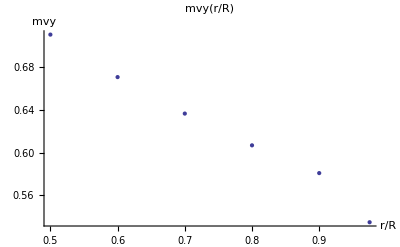
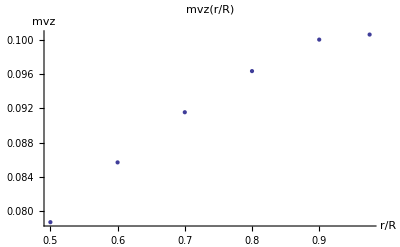
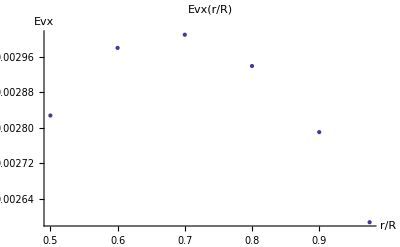
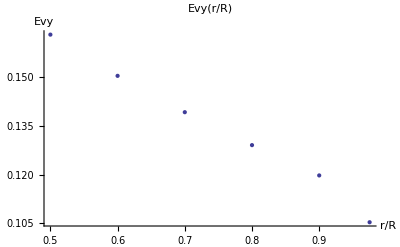
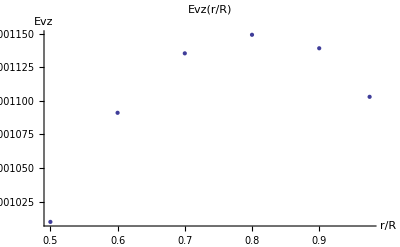
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

"F(r)=r; Re=50"

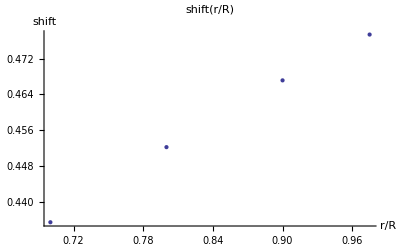
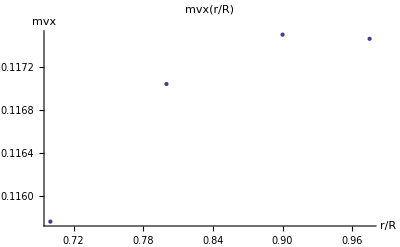
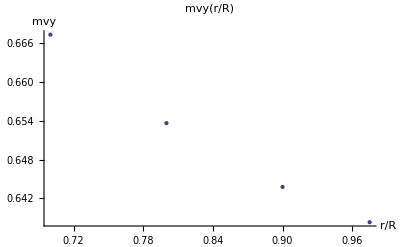
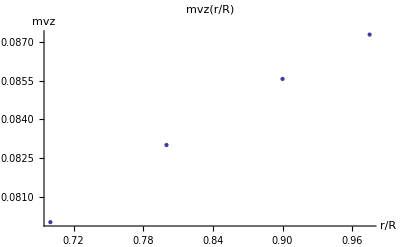
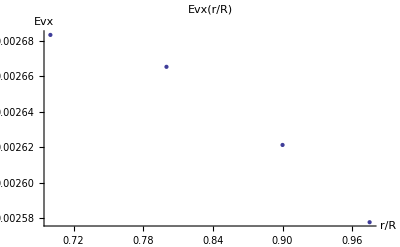
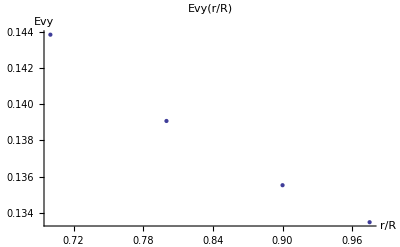
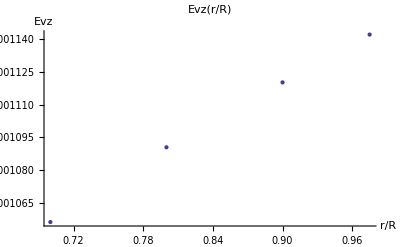
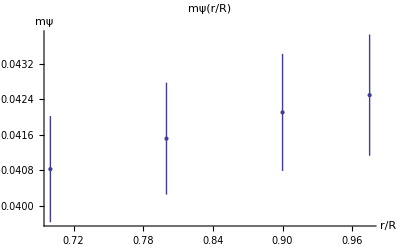

"F(r)=dp; Re=50"

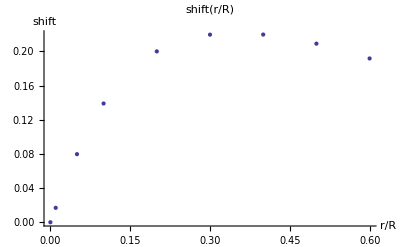
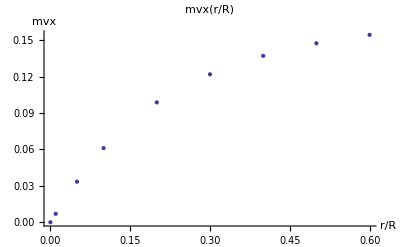
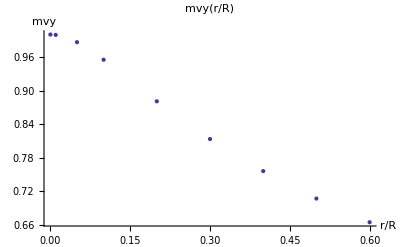
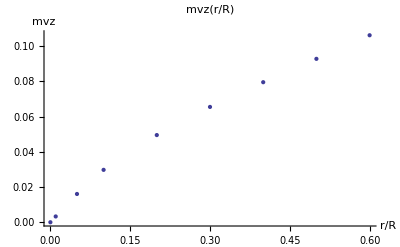
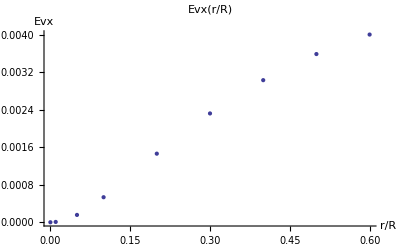
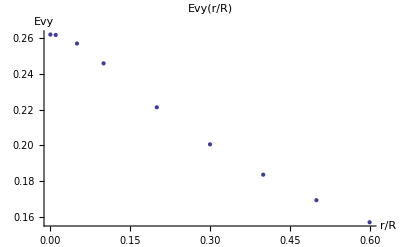
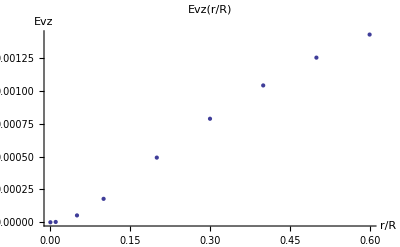
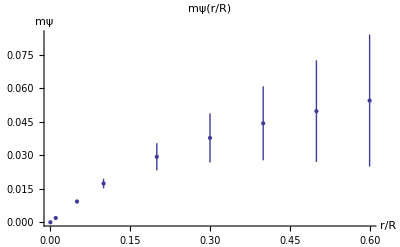

"F(r)=1"; Re=80

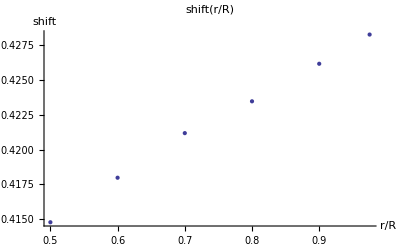
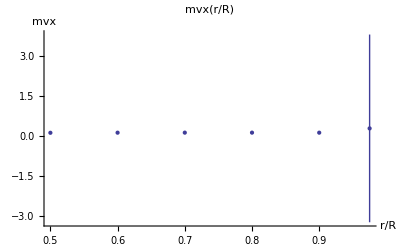
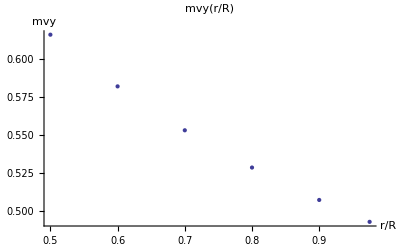
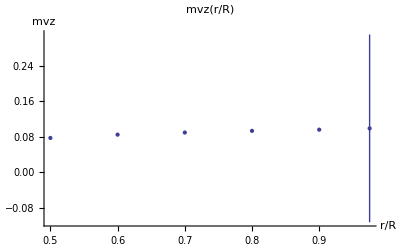
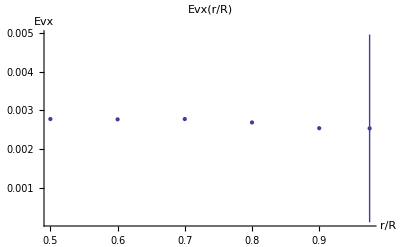
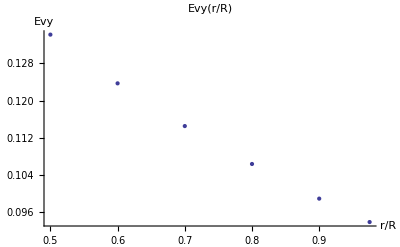
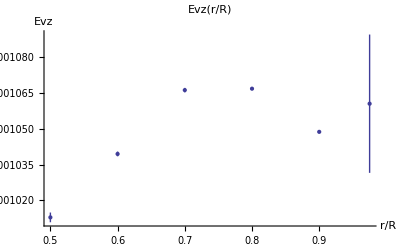
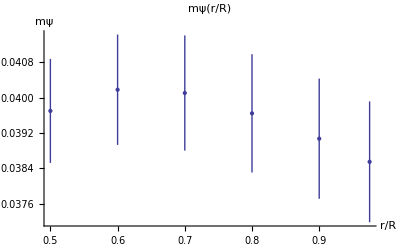

"F(r)=dp"; Re=80

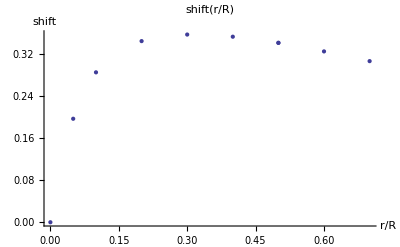
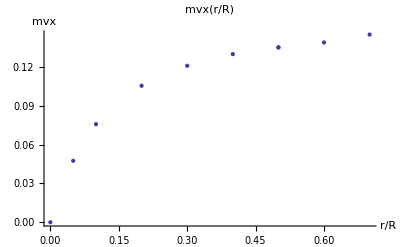
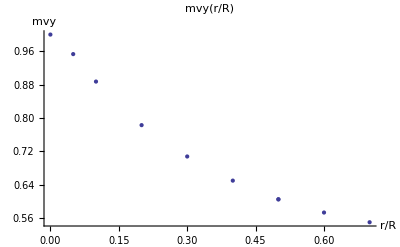
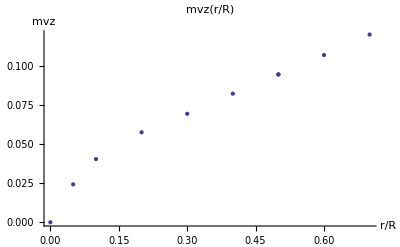
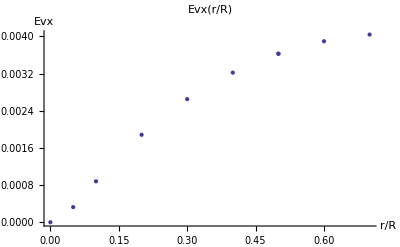
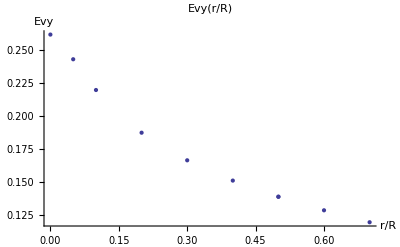
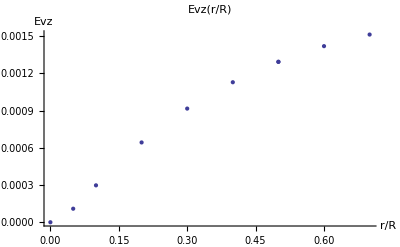
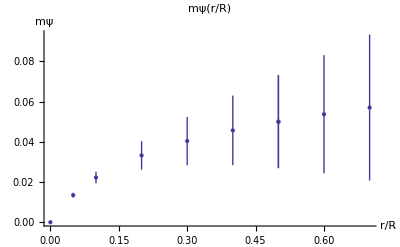

#### Подбор результатов

```mathematica
funcs={};
Block[{allbut=GetResults[{},False]},
numpar=First[Flatten[Position[fields,"Re"]]];
{"All such parameters=",PopupView[Union[(#1⟦numpar⟧&)/@allbut]]};
Manipulate[
TableForm[{(res=Reap[CheckboxBar[Dynamic[funcs],Thread[ShowDependanceMod["r/R",allfuncs,{"F(r)"->Fr,"Re"->R}]->allfuncs]],_])[[1]],Dynamic[Show[Append[-Graphics-,ImageSize->Large],funcs]]}]
,{R,Union[(#1⟦numpar⟧&)/@allbut],ControlType->PopupMenu},{Fr,{"dp","1","r"}}]
]
```

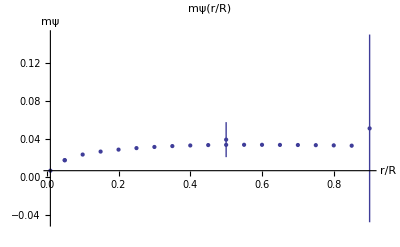
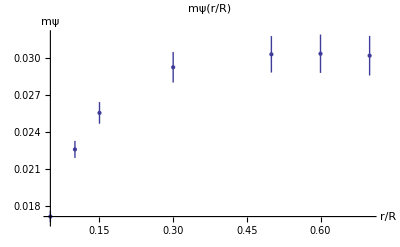
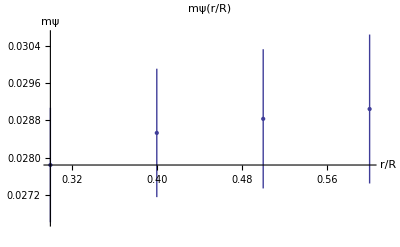

```mathematica
funcs
```

```mathematica
funcs[[1,2]]
```

{AxesLabel→{r/R, shift},AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→{r/R, shift},AxesOrigin→{0.,0.},Method→{},PlotLabel→ shift(r/R),PlotRangeClipping→True}

```mathematica
grs=ListPlot[Sort/@ExtractList/@funcs,PlotMarkers->Automatic,PlotLegends->PointLegend[{"Pressure gradient","Constant force","Centrifugal force"},LegendFunction->"Frame",LegendLabel->"Forcings:"],AxesOrigin->{0,0},PlotRange->{{0,1},All},Sequence@@funcs[[1,2]]]
```

```mathematica
{ListPlot[ExtractList[funcs[[1]]],PlotMarkers->{■},PlotLabel->"Pressure gradient"],ListPlot[ExtractList[funcs[[2]]],PlotLabel->"Constant force"],ListPlot[ExtractList[funcs[[3]]],PlotMarkers->{◆},PlotLabel->"Centrifugal force"]}
```

```mathematica
Export["d:\\psik@200.eps",grs];
```

```mathematica
funcs={};
Block[{allbut=GetResults[{},False]},
 numpar=First[Flatten[Position[fields,"r/R"]]];
 {"All such parameters=",PopupView[Union[(#1⟦numpar⟧&)/@allbut]]};
 Manipulate[
  TableForm[ {(res=Reap[CheckboxBar[Dynamic[funcs],Thread[ShowDependanceMod["Re",allfuncs,{"F(r)"->Fr,"r/R"->r}]->allfuncs]],_])[[1]],Dynamic[Show[Insert[-Graphics-,ImageSize->Large,2],funcs]]}]
  ,{r,Union[(#1⟦numpar⟧&)/@allbut],ControlType->PopupMenu},{Fr,{"dp","1","r"}}]
 ]
```

```mathematica
grs=ListPlot[Sort/@ExtractList/@funcs,PlotMarkers->Automatic,PlotLegends->PointLegend[{"Pressure gradient","Constant force","Centrifugal force"},LegendFunction->"Frame",LegendLabel->"Forcings:"],AxesOrigin->{0,0},PlotRange->{{0,300},All},Sequence@@funcs[[1,2]]]
```

```mathematica
Export["d:\\psiRe@0,05.eps",grs];
```

```mathematica
Block[{allbut=GetResults[{"F(r)"->"dp"}]},
numpar=First[Flatten[Position[fields,"Re"]]];
funcs=.;
DynamicModule[{Relist=Union[(#1⟦numpar⟧&)/@allbut],x=Graphics[{},ImageSize->100,AspectRatio->1/GoldenRatio],nR,types,
g=Table[Plot[Sin[n x],{x,0,2π},ImageSize->100,Ticks->None],{n,3}]},
{PopupView[Relist,Dynamic[nR]],CheckboxBar[Dynamic[types],{"dp","1","epsr"}],CheckboxBar[Dynamic[funcs],Thread[ShowDependance["r/R",allfuncs,{"F(r)"->"dp","Re"->100}]->allfuncs]],{Dynamic[Relist⟦nR⟧],Dynamic[funcs]}}
]]
```

```mathematica
ShowDependance["Re",allfuncs,{"F(r)"->"1"}]
```

All data matches (True):

All such parameters={10,20,30,40,50,60,70,80,90,100,110,128,256}

{Re,r/R,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Re→1,r/R→0.25,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=11

№2:{Re→150,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№3:{Re→100,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№4:{Re→90,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№5:{Re→80,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№6:{Re→10,r/R→0.05,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№7:{Re→70,r/R→0.1,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№8:{Re→70,r/R→0,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№9:{Re→40,r/R→0.2,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№10:{Re→40,r/R→0.1,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

So constant parameters are:

{Re→1,r/R→0.25,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

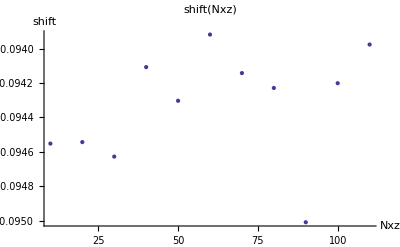
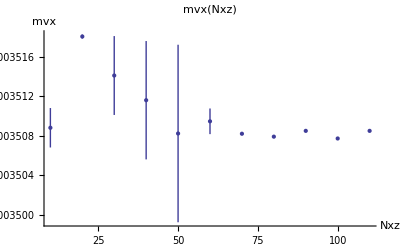
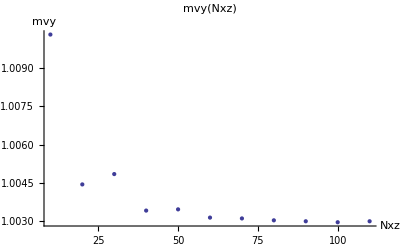
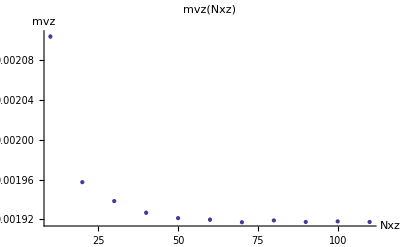
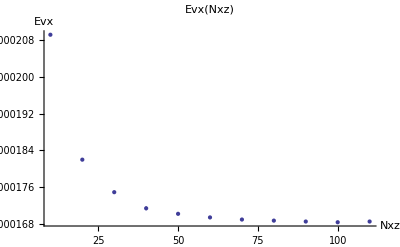
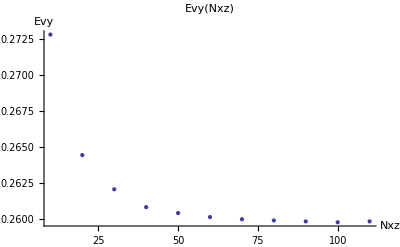
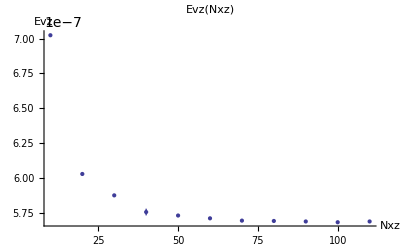
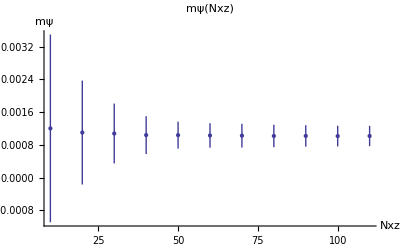

```mathematica
ShowDependance["Nxz",allfuncs]
```

```mathematica
pts//TableForm
```

```mathematica
Export[ToString[Unique[]]<>".eps",#]&/@{}
```

{$17.eps,$18.eps,$19.eps,$20.eps,$21.eps,$22.eps,$23.eps,$24.eps}

### Отдельное рисование

```mathematica
numfunc=4;
```

```mathematica
list=(Transpose[{First/@pts,{#⟦1⟧,#⟦2⟧}&/@(#[[numfunc]]&/@pts)}];
Transpose[{(1/First[#])^-1&/@pts,First[#]&/@(#[[numfunc]]&/@pts)}])
```

```mathematica
ListPlot[Drop[list,2],PlotRange->All,PlotLabel->Last[Last[(#1⟦numfunc⟧&)/@pts]],PlotStyle->PointSize[0.03]]
```

```mathematica
Transpose[pts[[All,2;;-2]]]
```

```mathematica
With[{param="lfi"},ListPlot[Transpose[{First/@pts,First/@#}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")"]&/@Transpose[pts[[All,2;;-2]]]
]
```

```mathematica
Transpose[{First/@pts,First/@pts[[All,8]]}]
```

{{0.01,3.66375},{0.1,0.00100646},{1.,0.00100646},{2 π,0.00100646}}

```mathematica
ListPlot[Rest@Transpose[{First/@pts,First/@pts[[All,8]]}]]
```

```mathematica
ListPlot[(First/@pts[[All,5]])]
```

```mathematica
With[{param="Re"},ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All]&/@Transpose[pts[[All,2;;-2]]]
]
```

```mathematica
Fit[Drop[list,2],{1,x},x]
```

0.990812+2.49089 x

```mathematica
PrintRange[GetFields[#,{"Re","shift"}]&/@$res]
```